```mathematica
Clear["Global`*"]
```

```mathematica
imag=y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;

real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
```

```mathematica
re1= Normal[Series[real,{y,0,2}]];
```

```mathematica
im1= Normal[Series[imag,{y,0,2}]];
```

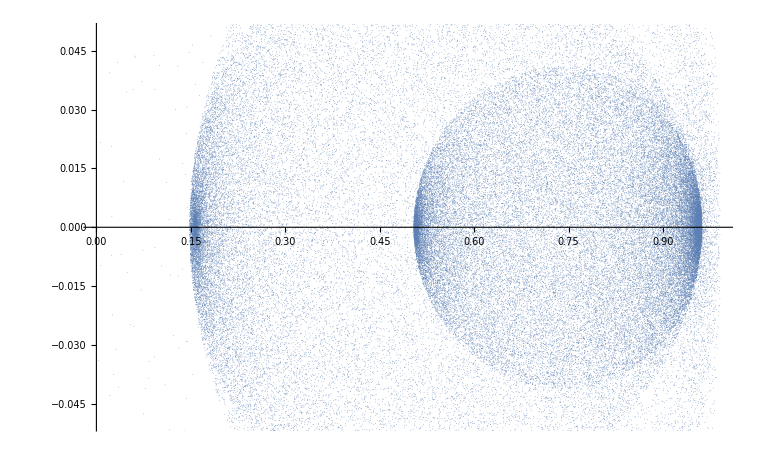
```mathematica
nuvem=Show[-Graphics-,Frame-> True];
```

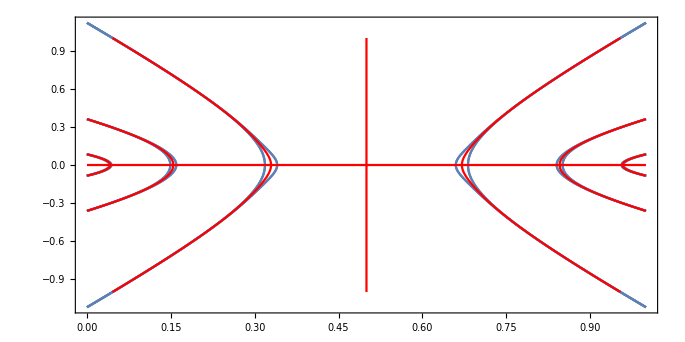
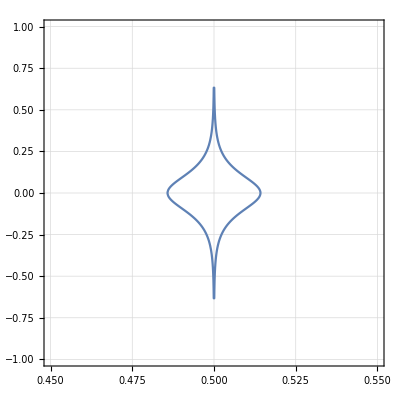
```mathematica
bands=Show[-Graphics-,-Graphics-];
```

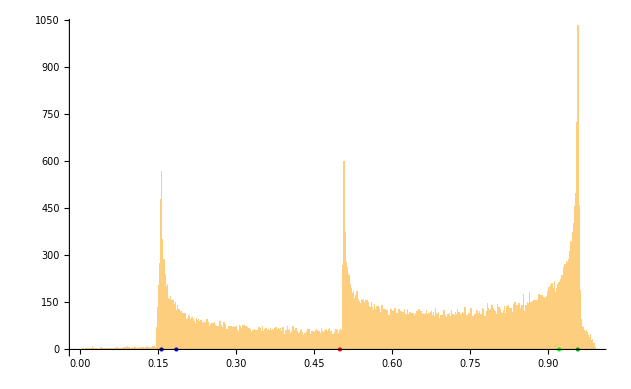
```mathematica
hist=-Graphics-;
```

```mathematica
lista3=Solve[xn1==re1/. y->-(yn1/((-1+2 x) μ^3 (1-2 x μ+2 x^2 μ-2 x μ^2+2 x^2 μ^2+6 x^2 μ^3-12 x^3 μ^3+6 x^4 μ^3-4 x^3 μ^4+12 x^4 μ^4-12 x^5 μ^4+4 x^6 μ^4))),x];
```

Se a derivada 2a é pequena (em módulo), então há mais pontos no eixo vertical do gráfico acima próximos ao mínimo, ou seja, uma faixa maior de pontos do Domínio é levada a uma pequena região na Imagem

```mathematica
{2/187.5481604163051,1/70.31370168640979,2/91.53558889912892+2/658.6570527658623}
```

{0.0106639,0.014222,0.0248859}

```mathematica
DSPlot=ListPlot[Table[{x,100Sum[Abs[D[lista3⟦s,1,2⟧,xn1]/. {μ-> 3.8283,yn1-> 0,xn1-> x}],{s,1,22}]},{x,0.1,1,1/303}],PlotRange->All,Frame->True,Joined->True,GridLines->Automatic];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

$Aborted

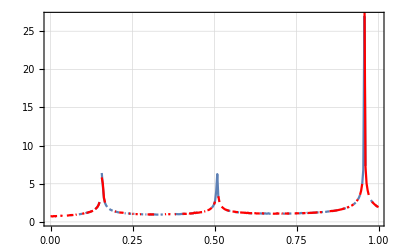

```mathematica
Show[DSPlot,ListPlot[Table[{x,Sum[Abs[D[lista3⟦s,1,2⟧,xn1]/. {μ-> 3.828,yn1-> 0,xn1-> x}],{s,1,22}]},{x,0,1,1/301}],PlotRange->All,Frame->True,Joined->True,GridLines->Automatic,PlotStyle->Red]]
```

```mathematica
Dmap3=D[real/.y-> 0,x];
```

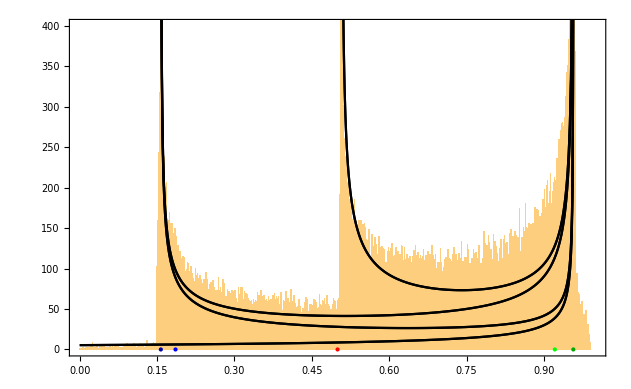

```mathematica
Show[hist,ParametricPlot[{real/. {μ-> 3.8283,y-> 0},300Abs[1/Dmap3]/. {μ-> 3.8283}},{x,0,1},MaxRecursion-> 10,AspectRatio->1/2,PlotStyle->Black,PlotRange->{0,10}],Frame->True,PlotRange-> {{0,1},{0,400}}]
```

```mathematica
xs = Solve[imag==0,x];
y3null=Sort[xs/.{y-> 0,μ-> 3.8283}]
```

{{x→0.0421228},{x→0.154466},{x→0.329308},{x→1/2},{x→0.670692},{x→0.845534},{x→0.957877}}

```mathematica
f = 5
f1 =Interpolation[Table[{real/. {μ-> 3.8283,y-> 0},Abs[1/Dmap3]/. {μ-> 3.8283}},{x,0,(1-10^-f)y3null⟦1,1,2⟧,0.0001}]];
f2 =Interpolation[Table[{real/. {μ-> 3.8283,y-> 0},Abs[1/Dmap3]/. {μ-> 3.8283}},{x,(1+10^-f)y3null⟦1,1,2⟧,(1-10^-f)y3null⟦2,1,2⟧,0.0001}]];
f3 =Interpolation[Table[{real/. {μ-> 3.8283,y-> 0},Abs[1/Dmap3]/. {μ-> 3.8283}},{x,(1+10^-f)y3null⟦2,1,2⟧,(1-10^-f)y3null⟦3,1,2⟧,0.0001}]];
f4 =Interpolation[Table[{real/. {μ-> 3.8283,y-> 0},Abs[1/Dmap3]/. {μ-> 3.8283}},{x,(1+10^-f)y3null⟦3,1,2⟧,(1-10^-f)y3null⟦4,1,2⟧,0.0001}]];
```

5

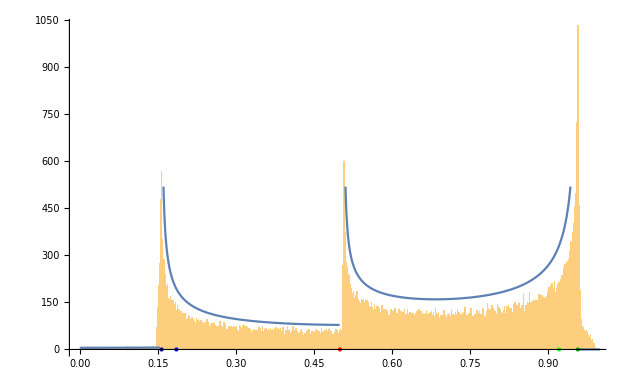

```mathematica
Show[hist,Plot[300pesototal[x],{x,0,1}, MaxRecursion->5]]
```

```mathematica
NI
```

```mathematica
pesototal[x_] = Piecewise[{{f1[x],x≤ 0.15727615898799918},{f1[x]+f2[x]+f3[x],0.15727615898799918<x≤ 0.5074039373682595},{f1[x]+f2[x]+f3[x]+f4[x],0.5074039373682595< x≤ 0.9570750000148109}}];
```

```mathematica
NIntegrate[pesototal[x]x,{x,0,0.9570750000148109}, Exclusions->{0.15727615898799918,0.5074039373682595,0.9570750000148109},MaxRecursion->50]/NIntegrate[pesototal[x],{x,0,0.9570750000148109},Exclusions->{0.15727615898799918,0.5074039373682595,0.9570750000148109},MaxRecursion->50]
```

0.63927

```mathematica
pesototal[0.500001]
```

InterpolatingFunction::dmval: Input value {0.500001} lies outside the range of data in the interpolating function. Extrapolation will be used.

638.837

```mathematica
NIntegrate[pesototal[x],{x,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.95706691169764623746271322863449215745390574738848954439163208008}. NIntegrate obtained 0.536575 and 0.00102842 for the integral and error estimates.

0.536575

```mathematica
PesoTotalIntegrado[xinf_, xsup_] := Which[xinf < xsup< 0.1544,Integrate[f1[x],{x,xinf,xsup}],

xinf <0.1544 && 0.1544<xsup< 0.499,
Integrate[f1[x],{x,xinf,xsup}]+Integrate[f2[x],{x,0.1546,xsup}]+Integrate[f3[x],{x,0.1546,xsup}],

xinf <0.1544 && 0.501<xsup< 0.957,Integrate[f1[x],{x,xinf,xsup}]+Integrate[f2[x],{x,0.1546,xsup}]+Integrate[f3[x],{x,0.1546,xsup}] + Integrate[f4[x],{x,0.501,xsup}],

xinf ≥ 0.1544 && 0.1544<xsup< 0.499,
Integrate[f1[x],{x,xinf,xsup}]+Integrate[f2[x],{x,xinf,xsup}]+Integrate[f3[x],{x,xinf,xsup}],

xinf ≥ 0.1544 && 0.501<xsup< 0.957,
Integrate[f1[x],{x,xinf,xsup}]+Integrate[f2[x],{x,xinf,xsup}]+Integrate[f3[x],{x,xinf,xsup}] + Integrate[f4[x],{x,0.501,xsup}],

xinf≥ 0.501 && xsup < 0.957, Integrate[f1[x],{x,xinf,xsup}]+Integrate[f2[x],{x,xinf,xsup}]+Integrate[f3[x],{x,xinf,xsup}] + Integrate[f4[x],{x,xinf,xsup}]]
```

```mathematica
PesoTotalIntegrado[0.1,0.48]
```

InterpolatingFunction::dmval: Input value {8} lies outside the range of data in the interpolating function. Extrapolation will be used.

Integrate::ilim: Invalid integration variable or limit(s) in {8,0.1,0.48}.

InterpolatingFunction::dmval: Input value {8} lies outside the range of data in the interpolating function. Extrapolation will be used.

Integrate::ilim: Invalid integration variable or limit(s) in {8,0.1546,0.48}.

InterpolatingFunction::dmval: Input value {8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {8,0.1546,0.48}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

∫_0.1^0.48 6.66337×10^18ⅆ8+∫_0.1546^0.48 5.01856×10^21ⅆ8+∫_0.1546^0.48 9.6302×10^30ⅆ8

```mathematica
PesoTotalIntegrado[0,0.16]
```

If[0<0.0238394 And<0.16,∫_0^0.16 f1[x]ⅆx,None]

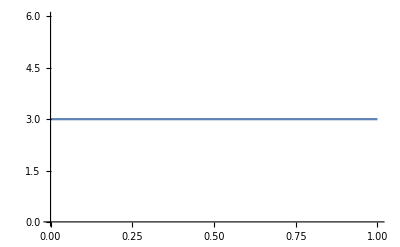

```mathematica
Plot[y = 3,{y,0,1}]
```